```mathematica
(*FastICA Laplace *)
x=RandomVariate[LaplaceDistribution[0,1],10000];
y=RandomVariate[LaplaceDistribution[0,1],10000];
A={{5,10},{10,2}};
mt=A.{x,y};
mt=mt-Mean[Transpose[mt]];
```

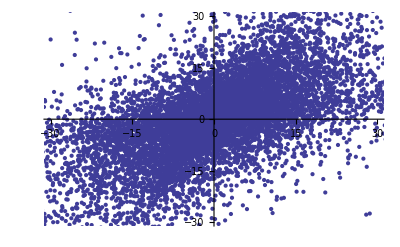

```mathematica
ma=Transpose[mt];
ListPlot[{ma[[All]]},PlotRange->{{-30,30},{-30,30}}]
```

```mathematica
Covariance[Transpose[mt]]
```

{{255.234,143.474},{143.474,210.658}}

```mathematica
Eigenvalues[Covariance[Transpose[mt]]]
```

{378.14,87.7513}

```mathematica
Eigenvectors[Covariance[Transpose[mt]]]
```

{{-0.759442,-0.650575},{0.650575,-0.759442}}

```mathematica
d12=1/Sqrt[Eigenvalues[Covariance[Transpose[mt]]][[1]]]
d22=1/Sqrt[Eigenvalues[Covariance[Transpose[mt]]][[2]]]
dmat=DiagonalMatrix[{d12,d22}]
```

0.0514249

0.106751

{{0.0514249,0.},{0.,0.106751}}

```mathematica
emat=Transpose[Eigenvectors[Covariance[Transpose[mt]]]]
```

{{-0.759442,0.650575},{-0.650575,-0.759442}}

```mathematica
vmat=emat.dmat.Transpose[emat]
```

{{0.0748417,-0.0273353},{-0.0273353,0.0833345}}

```mathematica
x=RandomVariate[LaplaceDistribution[0,1],10000];
y=RandomVariate[LaplaceDistribution[0,1],10000];
mt=A.{x,y};
mt=mt-Mean[Transpose[mt]];
```

```mathematica
zmat=vmat.mt;
```

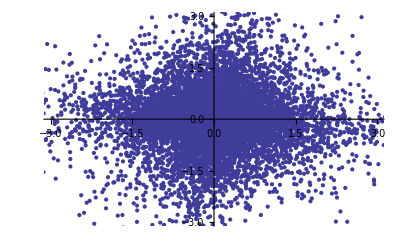

```mathematica
za=Transpose[zmat];
ListPlot[{za[[All]]},PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
w={1,0};
(*w={2,20};//N*)
(*w=w/Norm[w]//N*)
epsilon=0.00001;
n=Length[x];
cnt=1;
wbefore=w;
While[cnt<n,
wbefore=w;
w=(1/n)*Sum[((w.zmat[[All,i]])^3)*zmat[[All,i]],{i,1,n}]-3*w;
w=w/Norm[w];
Print["cnt=",cnt];
Print["w=",w];

If[1-epsilon<=Abs[w.wbefore]&& Abs[w.wbefore]<=1+epsilon,
Print["収束した:"];
Print["w=",w];
Print["cnt=",cnt];
Print["Abs[w.wbefore]=",Abs[w.wbefore]];
cnt=n;
];
++cnt;
]
Kurtosis[w.zmat]-3
```

cnt=1

w={0.983819,-0.179163}

cnt=2

w={0.985055,-0.172242}

cnt=3

w={0.984997,-0.172574}

収束した:

w={0.984997,-0.172574}

cnt=3

Abs[w.wbefore]=1.

3.70512

```mathematica
(* True Value*)
tmat=vmat.A;
truemat={};
i=1;
While[i≤2,
truemat=Append[truemat,tmat[[All,i]]/Norm[tmat[[All,i]]]];
i++;
];
truemat=Transpose[truemat];
MatrixForm[truemat]
```

(0.143274 | 0.988382
0.989683 | -0.151993)

```mathematica
w=RandomReal[{-Sqrt[3],Sqrt[3]},2];
(*w={1,0};*)

(*w={2,20};//N*)

(*w=w/Norm[w]//N*)
epsilon=0.00001;
n=Length[x];
cnt=1;
wbefore=w;
While[cnt<n,
wbefore=w;
w=(1/n)*Sum[((w.zmat[[All,i]])^3)*zmat[[All,i]],{i,1,n}]-3*w;
w=w/Norm[w];
Print["cnt=",cnt];
Print["w=",w];
If[1-epsilon<=Abs[w.wbefore]&& Abs[w.wbefore]<=1+epsilon,
Print["収束した:"];
Print["w=",w];
Print["cnt=",cnt];
Print["Abs[w.wbefore]=",Abs[w.wbefore]];
cnt=n;
];
++cnt;
]
Kurtosis[w.zmat]-3
```

cnt=1

w={-0.818171,0.574974}

cnt=2

w={-0.970397,0.241515}

cnt=3

w={-0.985478,0.169801}

cnt=4

w={-0.984976,0.172692}

収束した:

w={-0.984976,0.172692}

cnt=4

Abs[w.wbefore]=0.999996

3.70511

```mathematica
MatrixForm[truemat]
```

(0.143274 | 0.988382
0.989683 | -0.151993)